```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
```

```mathematica
Solve[(up1-2u0+um1)/(dt^2)+3H0 (up1 - um1)/(2dt)+k^2/a0^2 u0==T0/a0^2,up1]//Simplify
```

{{up1→(2 dt^2 (T0-k^2 u0)+2 a0^2 (2 u0-um1)+3 a0^2 dt H0 um1)/(a0^2 (2+3 dt H0))}}

```mathematica
(1/(64Pi G)/((2Pi)^3L^3))/ρ//Simplify
(16Pi G dV)^2*%/.{ρ->3H^2/(8Pi G),dV->3H0^2/(8Pi G)}
```

1/(512 G L^3 π^4 ρ)

(3 H0^4)/(16 H^2 L^3 π^3)

```mathematica
(k^3/(64Pi G)/((2Pi)^3L^3))/ρ/((H0/β)^2)//Simplify
(16Pi G dV)^2*%/.{ρ->3H^2/(8Pi G),dV->3H0^2/(8Pi G)}
```

(k^3 β^2)/(512 G H0^2 L^3 π^4 ρ)

(3 H0^2 k^3 β^2)/(16 H^2 L^3 π^3)

```mathematica
β0 =10.;
```

```mathematica
bubble = ReadList[NotebookDirectory[]<>"B_beta_"<>ToString[NumberForm[β0,{3,2}]]<>"_gammaperbeta_0.00_j_1.dat",Table[Number,{4}]];
bubble[[All,3]] = bubble[[All,3]]*bubble[[All,4]];
```

```mathematica
bounds = {Min@#,Max@#}&@bubble[[All,3]];
invmollweide[{x_,y_}]:=With[{theta=ArcSin[y]},{Pi x/(2 Cos[theta]),ArcSin[(2 theta+Sin[2 theta])/Pi]}]
Legended[ImageTransformation[ListDensityPlot[Join[{Mod[#[[2]],2Pi]-Pi,#[[1]]+Pi/2,#[[3]]}&/@bubble,{Mod[#[[2]],2Pi]-Pi,#[[1]]-3Pi/2,#[[3]]}&/@bubble,{Mod[#[[2]],2Pi]-Pi,#[[1]]-Pi/2,#[[3]]}&/@bubble],PlotRange->{{-Pi,Pi},{-Pi/2,Pi/2},All},PlotRangePadding->None,Frame->None,ImagePadding->None,ColorFunction->"Rainbow",AspectRatio->1/2,ImageSize->600],invmollweide,DataRange->{{-Pi,Pi},{-Pi/2,Pi/2}},PlotRange->{{-2,2},{-1,1}},Masking->All,Background->White],BarLegend[{"Rainbow",bounds},LegendLabel->Style["βa_cR_c",Black,14],LegendMarkerSize->160,LabelStyle->{Black,FontSize-> 12,FontFamily->"Times"}]]
```

-Graphics-

```mathematica
Ωlist = Table[ReadList[NotebookDirectory[]<>"OmegaGW_beta_"<>ToString[NumberForm[β0,{3,2}]]<>"_gammaperbeta_0.00_j_"<>ToString@index<>".dat",Table[Number,5]],{index,{1,3}}];
Ωlist = Table[GatherBy[Ωlist[[js]],First],{js,Length@Ωlist}];
LLΩk1 = Table[Interpolation[Log10@{#[[2]],Max[#[[3]],1.*^-32]}&/@Mean[Ωlist[[All,jt]]],InterpolationOrder->1],{jt,Length[Ωlist[[1]]]}];
LLΩk2 = Table[Interpolation[Log10@{#[[2]],Max[#[[4]],1.*^-32]}&/@Mean[Ωlist[[All,jt]]],InterpolationOrder->1],{jt,Length[Ωlist[[1]]]}];
LLΩk3 = Table[Interpolation[Log10@{#[[2]],Max[#[[5]],1.*^-32]}&/@Mean[Ωlist[[All,jt]]],InterpolationOrder->1],{jt,Length[Ωlist[[1]]]}];
```

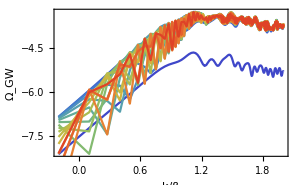
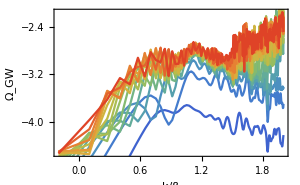
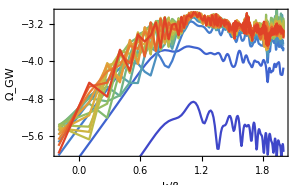

```mathematica
Row@{Show[Plot[LLΩk1[[-1]][x]//Evaluate,{x,LLΩk1[[-1]][[1,1,1]],LLΩk1[[-1]][[1,1,2]]},PlotStyle->None],Plot[#[x]&/@LLΩk1//Evaluate,{x,LLΩk1[[-1]][[1,1,1]],LLΩk1[[-1]][[1,1,2]]},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,20])],ImageSize->300,FrameLabel->{"k/β","Ω_GW"}],
Show[Plot[LLΩk2[[-1]][x]//Evaluate,{x,LLΩk1[[-1]][[1,1,1]],LLΩk1[[-1]][[1,1,2]]},PlotStyle->None],Plot[#[x]&/@LLΩk2//Evaluate,{x,LLΩk1[[-1]][[1,1,1]],LLΩk1[[-1]][[1,1,2]]},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,20])],ImageSize->300,FrameLabel->{"k/β","Ω_GW"}],
Show[Plot[LLΩk3[[-1]][x]//Evaluate,{x,LLΩk1[[-1]][[1,1,1]],LLΩk1[[-1]][[1,1,2]]},PlotStyle->None],Plot[#[x]&/@LLΩk3//Evaluate,{x,LLΩk1[[-1]][[1,1,1]],LLΩk1[[-1]][[1,1,2]]},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,20])],ImageSize->300,FrameLabel->{"k/β","Ω_GW"}]}
```

```mathematica
ρlist = Table[ReadList[NotebookDirectory[]<>"OmegaTotGW_beta_"<>ToString[NumberForm[β0,{3,2}]]<>"_gammaperbeta_0.00_j_"<>ToString@index<>".dat",Table[Number,5]],{index,{1,3}}];
ρt = Table[{Interpolation[{#[[1]],#[[3]]}&/@ρlist[[j]],InterpolationOrder->1],Interpolation[{#[[1]],#[[4]]}&/@ρlist[[j]],InterpolationOrder->1],Interpolation[{#[[1]],#[[5]]}&/@ρlist[[j]],InterpolationOrder->1]},{j,Length@ρlist}];
```

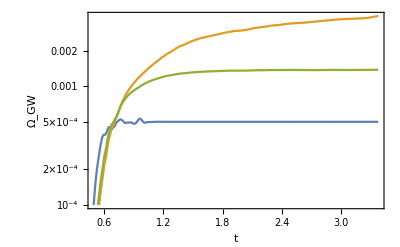

```mathematica
LogPlot[{Mean[#[[1]][t]&/@ρt],Mean[#[[2]][t]&/@ρt],Mean[#[[3]][t]&/@ρt]}//Evaluate,{t,ρt[[1,1,1,1,1]],ρt[[1,1,1,1,2]]},FrameLabel->{"t","Ω_GW"},PlotRange->{All,{1.*^-4,All}}]
```

```mathematica
Ωlist = Table[ReadList[NotebookDirectory[]<>"OmegaGWfin_beta_"<>ToString[NumberForm[β0,{3,2}]]<>"_gammaperbeta_0.00_j_"<>ToString@index<>".dat",Table[Number,4]],{index,{1,3}}];
```

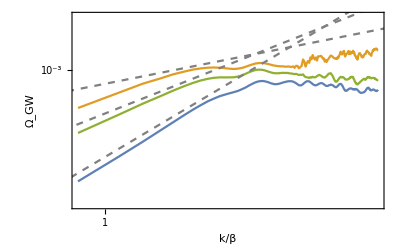

```mathematica
Show[ListPlot[{{#[[1]],#[[2]]}&/@Log10@Mean@Ωlist,{#[[1]],#[[3]]}&/@Log10@Mean@Ωlist,{#[[1]],#[[4]]}&/@Log10@Mean@Ωlist},Joined->True,PlotRange->{All,{-8,-1}}],LogLogPlot[{0.03x^1,0.01x^2,0.002x^3},{x,0.1,10},PlotStyle->Directive[Gray,Dashed]],FrameLabel->{"k/β","Ω_GW"},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}}]
```

```mathematica
D[au[τ[t]]/a[τ[t]],t]/.τ'[t]->1/a[τ[t]]
D[%,t]+3D[a[τ[t]],t]/a[τ[t]] % + k^2/a[τ[t]]^2au[τ[t]]/a[τ[t]]/.τ'[t]->1/a[τ[t]]/.au->U//Simplify//Expand
```

-(au[τ[t]] a'[τ[t]])/a[τ[t]]^3+au'[τ[t]]/a[τ[t]]^2

(k^2 U[τ[t]])/a[τ[t]]^3-(U[τ[t]] a''[τ[t]])/a[τ[t]]^4+U''[τ[t]]/a[τ[t]]^3

```mathematica
Simplify[First@DSolve[{τ'[t]==1/a[t]/.Last@DSolve[{a'[t]/a[t]==H0 (a0/a[t])^2,a[t0]==a0},a,t],τ[t0]==τ0},τ[t],t],{a0>0,H0>0}]
Last@DSolve[{a'[t]/a[t]==H0 (a0/a[t])^2,a[t0]==a0},a,t]
{(a'[t]/a[t])^2a[t]^4/a0^4,a[t]a''[t]+a'[t]^2}/.%//Simplify
```

{τ[t]→(-1+√(1+2 H0 t-2 H0 t0)+a0 H0 τ0)/(a0 H0)}

{a→Function[{t},√(a0^2 (1+2 H0 t-2 H0 t0))]}

{H0^2,0}

```mathematica
First@DSolve[{U''[τ]+k^2 U[τ]==0,U[0]==U0,U'[0]==dU0},U,τ]
```

{U→Function[{τ},(k U0 Cos[k τ]+dU0 Sin[k τ])/k]}

```mathematica
D[U[τ[t]]/a[t],t]^2/H^2/.{τ'[t]->1/a,τ[t]->τ}/.{a[t]->a,a'[t]->H a}//Simplify
%/.{U->Function[{τ},(k U0 Cos[k τ]+dU0 Sin[k τ])/k]}/.{a->a0 Sqrt[H0/H]}//Simplify
Integrate[%,{τ,0,2Pi/k}]/(2Pi/k)
Series[%,{H,0,0}]
```

(-a H U[τ]+U'[τ])^2/(a^4 H^2)

((k (dU0-a0 H √(H0/H) U0) Cos[k τ]-(a0 dU0 H √(H0/H)+k^2 U0) Sin[k τ])^2)/(a0^4 H0^2 k^2)

((a0^2 H H0+k^2) (dU0^2+k^2 U0^2))/(2 a0^4 H0^2 k^2)

(dU0^2+k^2 U0^2)/(2 a0^4 H0^2)+O[H]^1

```mathematica
(D[a[t[τ]]u[t[τ]],τ]^2+k^2(a[t[τ]]u[t[τ]])^2)/(2a0^4)/.{t'[τ]->a0,t[τ]->t}/.{a[t]->a0,a'[t]->H0 a0,u[t]->u0,u'[t]->du0}//Expand//FullSimplify
```

(k^2 u0^2+a0^2 (du0+H0 u0)^2)/(2 a0^2)